## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[6];
```

## Calculate T with forward difference method

### Manually integrate Schrodinger’s equation

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a,b,h}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a-m*h,b,h}]//N;

Return[xs];
]
```

```mathematica
yvec[k_,p_]:=Module[{n,m, h,cDiffCoeffs,numNonzero, nonZeroElements},
n=p["n"];
m=p["m"];
h = p["h"];

(*cDiffCoeffs={−1/12,4/3,−5/2,4/3,−1/12};*)
cDiffCoeffs={1,-2,1};

(*nonZeroElements={
n+m-2->-cDiffCoeffs[[1]],
n+m-1->-1*(
cDiffCoeffs[[1]]*Exp[Sqrt[2]*I*k*h]+
cDiffCoeffs[[2]]),
n+m->-1*(
cDiffCoeffs[[1]]*Exp[2*I*Sqrt[2]*k*h]+
cDiffCoeffs[[2]]*Exp[I*Sqrt[2]*k*h]+
cDiffCoeffs[[3]]+2h^2*k^2),
n+m+1->-1*(
cDiffCoeffs[[1]]*Exp[3*I*Sqrt[2]*k*h]+
cDiffCoeffs[[2]]*Exp[2*I*Sqrt[2]*k*h]+
(cDiffCoeffs[[3]]+h^2*2k^2)*Exp[I*Sqrt[2]*k*h]+
cDiffCoeffs[[4]])
};*)

nonZeroElements={
n+m->-cDiffCoeffs[[1]],
n+m+1->-1*(
cDiffCoeffs[[1]]*Exp[Sqrt[2]*I*k*h]+
cDiffCoeffs[[2]]+2*h^2*k^2)
};

Return[SparseArray[nonZeroElements,{n+m+1}]];
]
```

```mathematica
yvec[k,Association["a"->-10,"b"->10,"n"->5,"m"->2,"h"->"h"]]//MatrixForm
```

(0
0
0
0
0
0
-1
2-ⅇ^(ⅈ √2 h k)-2 h^2 k^2)

```mathematica
yvecKVec[kVec_,p_]:=Table[yvec[k,p],{k,kVec}]
```

```mathematica
D2Matrix[p_]:= Module[{n,m,cDiffCoeffs,bands},
n=p["n"];
m=p["m"];

(*cDiffCoeffs={−1/12,4/3,−5/2,4/3,−1/12};*)
cDiffCoeffs={1,-2,1};

bands=Table[Band[{1,i}]->cDiffCoeffs[[i]],{i,1,Length[cDiffCoeffs]}];

Return[SparseArray[bands,{1+n+m, 1+n+m}]];
];
```

```mathematica
D2Matrix[Association["n"->5,"m"->0]]//MatrixForm
```

(1 | -2 | 1 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 1 | -2
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
EMatrix[k_,p_]:=Module[{ n,m, h, band},
n=p["n"];
m=p["m"];
h = p["h"];

(*band = Band[{1,3}]->2*h^2*k^2;*)
band = Band[{1,2}]->2*h^2*k^2;
Return[SparseArray[band,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrixKVec[kVec_,p_]:=Table[EMatrix[k,p],{k,kVec}]
```

```mathematica
VMatrix[V_,Vparams_,p_]:=Module[{xg,n,m, h, u1V, matV},
(*xg=xgrid[p][[3;;-1]];*)
xg=xgrid[p][[2;;-1]];
n=p["n"];
m=p["m"];
h =p["h"];

(*These elements are constant for every value of k and should only be generated once per k value*)
(*u1V=Band[{m+1,m+3}]->2*h^2*V[xg];*)
u1V=Band[{m+1,m+2}]->2*h^2*V[xg,Vparams];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[matV];
];
```

```mathematica
kGrid[p_]:=Module[{kmin,kmax,numk,kh},
kmin=p["kmin"];
kmax=p["kmax"];
numk = p["numk"];
kh = (kmax-kmin)/(numk-1);

Return[Table[k,{k,kmin,kmax,kh}]];
];
```

```mathematica
psiSolutionKVec[V_,kVec_,p_,D2_,EMatrixVector_,yVector_]:=Module[{VV, soln},
VV = VMatrix[V,p];

soln = Table[{
kVec[[i]],
LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]]]
},{i,1, Length[kVec]}];
Return[soln];
];
```

```mathematica
psiSolutionKVecBindXGrid[V_,kVec_,p_,D2_,EMatrixVector_,yVector_]:=Module[{ xgfull,VV, soln}, 
xgfull=xgridFull[p];
VV=VMatrix[V,p];

soln = Table[{
kVec[[i]],
Transpose[{xgridFull[p],LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]], Method->"Banded"]}]
},{i,1, Length[kVec]}];
Return[soln];
];
```

### Test with sech^2 potential

```mathematica
V[x_]:=1/Cosh[x]^2;
params = Association["a"->-10, "b"->10,"n"->1000,"m"->100,"kmin"->0.01,"kmax"->2.001,"numk"->100];
params["h"]=(params["b"]-params["a"])/params["n"];
kgrid = kGrid[params];
```

```mathematica
d2mat = D2Matrix[params];
emat=EMatrixKVec[kgrid,params];
yyvec=yvecKVec[kgrid,params];
```

```mathematica
psiSol=psiSolutionKVecBindXGrid[V,kgrid,params,d2mat,emat,yyvec];
```

```mathematica
probabilities=Table[{ksol[[1]],Table[{xpsi[[1]],Abs[xpsi[[2]]]^2},{xpsi, ksol[[2]]}]},{ksol,psiSol}];
```

```mathematica
pltProbabilities[kindex_]:=ListPlot[{probabilities[[kindex,2]]},GridLines->Automatic,PlotLabel->"k="<>(probabilities[[kindex,1]]//ToString),Joined->True]
```

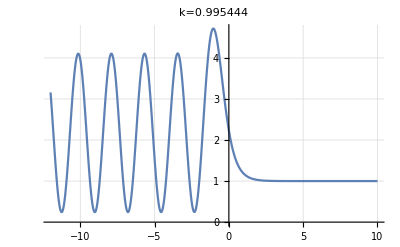

```mathematica
pltProbabilities[50]
```

#### Timing for 10,000 schrod solutions:

```mathematica
timingSolutions=Table[psiSolutionKVec[V,kgrid,params,d2mat,emat,yyvec],{i,1,100}]//Timing; (*100 solutions per iteration x 100 iterations = 10000 solutions*)
```

```mathematica
timingSolutions[[1]]
```

4.36824

here, timing is proportional to n+m ~ n

```mathematica
psiSolInterp=Interpolation[psiSol[[50,2]],InterpolationOrder->1]
```

InterpolatingFunction[{{-12., 10.}}, <>]

```mathematica
functest[x_]:=Exp[I*kgrid[[50]]*x]
```

```mathematica
err[sol_,mom_,x_]:=Module[{},
Abs[Conjugate[sol[x]]*
(sol''[x]
-2*params["h"]^2*V[x]*sol[x]
+params["h"]^2*mom^2*sol[x])]/
Abs[sol[x]]^2
]
```

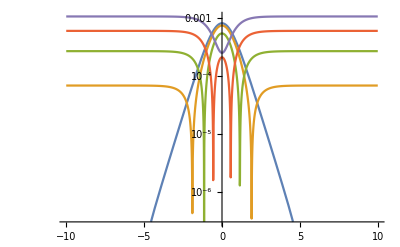

```mathematica
LogPlot[Evaluate[Table[err[psiSolInterp,kgrid[[ind]],x],{ind,1,100,20}]],{x,-10,10}]
```

## Calculate T

```mathematica
SchrEqOfV[V_,VParams_,kVec_,p_,D2_,EMatrixVector_,yVector_]:=Module[{VV, soln},
VV = VMatrix[V,VParams,p];

soln = Table[{
kVec[[i]],
LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]]]
},{i,1, Length[kVec]}];
Return[soln];
];
```

```mathematica
WaveFuncLeftOfV[V_, VParams_, SEDict_, k_,step_:1]:=Module[{a,b,c,help=SchrEqOfV[V,VParams,SEDict,k]},
a=SEDict["a"];
b=SEDict["b"];
c=SEDict["c"];
Fit[Table[Flatten[{x,f[x]/.help}],{x,a-c/k,a,step/k}],{Exp[I Sqrt[2]k x],Exp[-I Sqrt[2]k x]},x]
];
```